```mathematica
f[L_]:=FindRoot [Cos[x*L]-Cos[x]-2000.0*Sin[x]/(x),{x,803}]
```

```mathematica
x/.f[0.2]
```

801.106

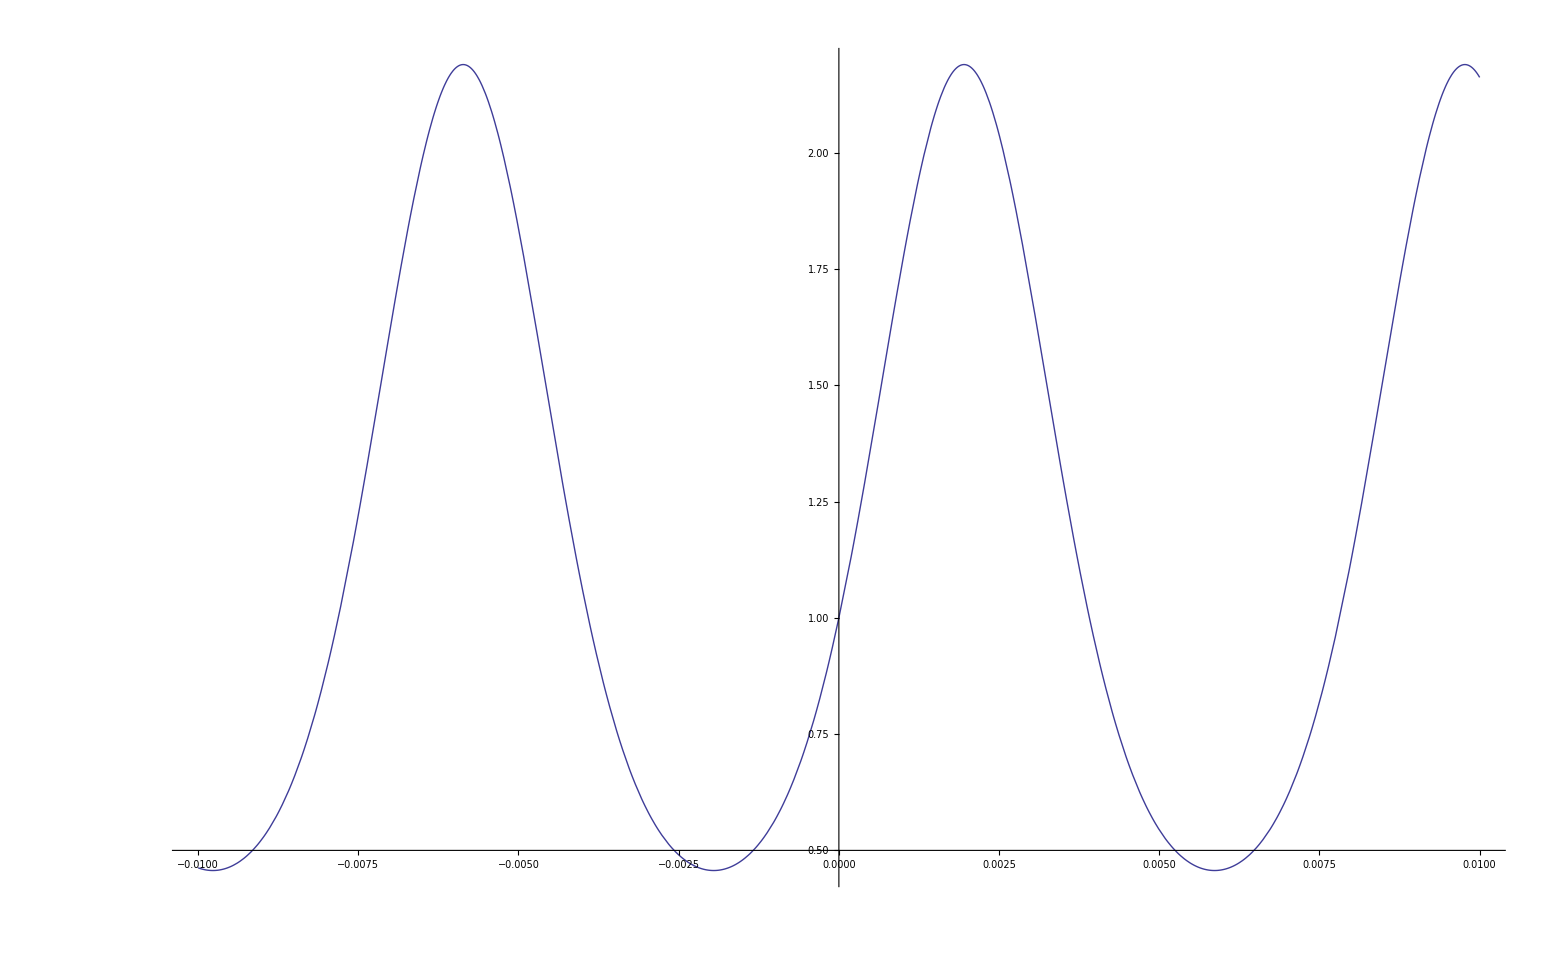

```mathematica
Plot[(Sin[(x/.f[L])*0.5*(1-L)])^2/(Sin[(x/.f[L])*0.5*(1+L)])^2,{L,-0.01, 0.01}]
```

```mathematica
[]
```

```mathematica
JurassicPark=ToRules[p2==0.0000001 && p1 ==0.00001 && p3 ==0.00001 && A==10000 &&z==256*3.141592653585]
```

{p2→1.×10^-7,p1→0.00001,p3→0.00001,A→10000,z→804.248}

```mathematica
(*Note this is for the single side pump case, which I have copied from the untitled 2 document.  t2 is g here *)
```

```mathematica
c[L_]:=(2 ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (4+(-1+ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L))) (x/.f[L])^2*A*A*p2 p3-2 ⅈ (x/.f[L])*A*(p2+p3)))/(ⅇ^(-2 ⅈ (x/.f[L])*L) (x/.f[L])^2*A*A*(2-ⅈ (x/.f[L])*A*p1) p2 p3+ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A*p1 (2+ⅈ (x/.f[L])*A*p2) p3+(x/.f[L])^2*A*A*p1 p2 (2-ⅈ (x/.f[L])*A*p3)+ⅈ ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A*p1) (2 ⅈ+(x/.f[L])*A*p2) (2 ⅈ+(x/.f[L])*A*p3)) /. JurassicPark
```

```mathematica
d[L_]:=(2 ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (x/.f[L])*A*(ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (2+ⅈ (x/.f[L])*A*p2) p3+p2 (2-ⅈ (x/.f[L])*A*p3)))/(-ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A*(2 ⅈ+(x/.f[L])*A*p1) p2 p3+ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A*p1 (-2 ⅈ+(x/.f[L])*A*p2) p3-(x/.f[L])^2*A*A*p1 p2 (2 ⅈ+(x/.f[L])*A*p3)+ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A*p1) (2 ⅈ+(x/.f[L])*A*p2) (2 ⅈ+(x/.f[L])*A*p3)) /. JurassicPark
```

```mathematica
e[L_]:=(4 ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A*p3))/(ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A*(2 ⅈ+(x/.f[L])*A*p1) p2 p3-ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A*p1 (-2 ⅈ+(x/.f[L])*A*p2) p3+(x/.f[L])^2*A*A*p1 p2 (2 ⅈ+(x/.f[L])*A*p3)-ⅇ^(-2 ⅈ(x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A*p1) (2 ⅈ+(x/.f[L])*A*p2) (2 ⅈ+(x/.f[L])*A*p3)) /. JurassicPark
```

```mathematica
g[L_]:=-(4 ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])*A*p3)/(ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A*(2 ⅈ+(x/.f[L])*A*p1) p2 p3-ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A*p1 (-2 ⅈ+(x/.f[L])*A*p2) p3+(x/.f[L])^2*A*A*p1 p2 (2 ⅈ+(x/.f[L])*A*p3)-ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A*p1) (2 ⅈ+(x/.f[L])*A*p2) (2 ⅈ+(x/.f[L])*A*p3)) /. JurassicPark
```

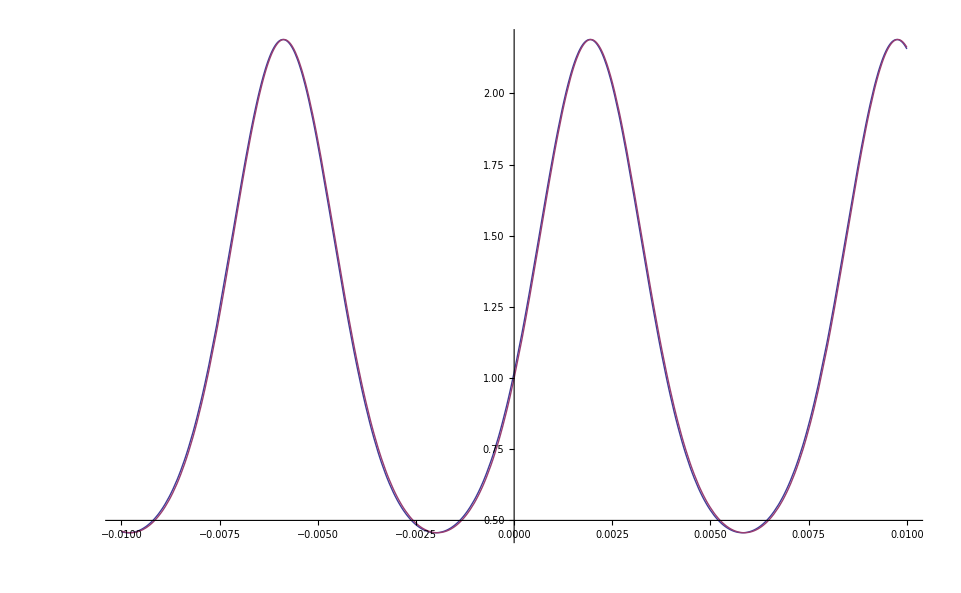

```mathematica
Plot[{(c[L]*(Conjugate[c[L]]) + d[L]*(Conjugate[d[L]])  )/(e[L]*(Conjugate[e[L]]) +g[L]*(Conjugate[g[L]]) ),(Sin[(x/.f[L])*0.5*(1-L)])^2/(Sin[(x/.f[L])*0.5*(1+L)])^2},{L,-0.01,0.01},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->16],FrameLabel->{"Length Difference ΔL (Units of L)","Amplitude Ratio"}]
```

```mathematica
f2[L_]:=p2*z*z*A*L  /. JurassicPark
```

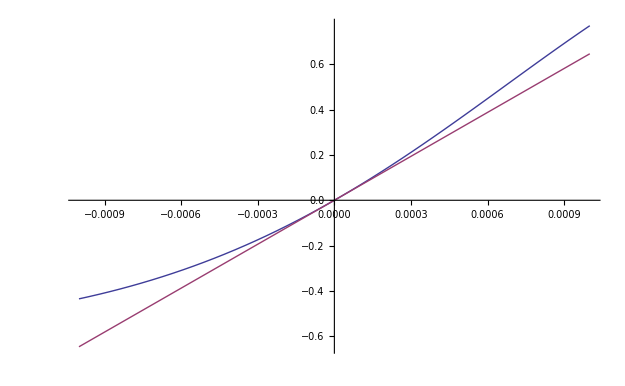

```mathematica
Plot[{(Sin[(x/.f[L])*0.5*(1-L)])^2/(Sin[(x/.f[L])*0.5*(1+L)])^2 -1,f2[L]},{L,-0.001,0.001}]
```

```mathematica
t2[L_]:=(8 ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)))/(ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A (2-ⅈ (x/.f[L])*A p1) p2 p3+ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A p1 (2+ⅈ (x/.f[L])*A p2) p3+(x/.f[L])^2*A*A p1 p2 (2-ⅈ (x/.f[L])*A p3)+ⅈ ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A p1) (2 ⅈ+(x/.f[L])*A p2) (2 ⅈ+(x/.f[L])*A p3)) /. JurassicPark
```

```mathematica
t1[L_]:=-(ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (x/.f[L])*A (ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A p1 p2 p3-ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (-2 ⅈ+(x/.f[L])*A p1) (-2 ⅈ+(x/.f[L])*A p2) p3+(-2 ⅈ+(x/.f[L])*A p1) p2 (2 ⅈ+(x/.f[L])*A p3)-ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) p1 (2 ⅈ+(x/.f[L])*A p2) (2 ⅈ+(x/.f[L])*A p3)))/(ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A (2 ⅈ+(x/.f[L])*A p1) p2 p3-ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A p1 (-2 ⅈ+(x/.f[L])*A p2) p3+(x/.f[L])^2*A*A p1 p2 (2 ⅈ+(x/.f[L])*A p3)-ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A p1) (2 ⅈ+(x/.f[L])*A p2) (2 ⅈ+(x/.f[L])*A p3)) /. JurassicPark
```

```mathematica
(*A plot of the phase of the exiting wave*)
```

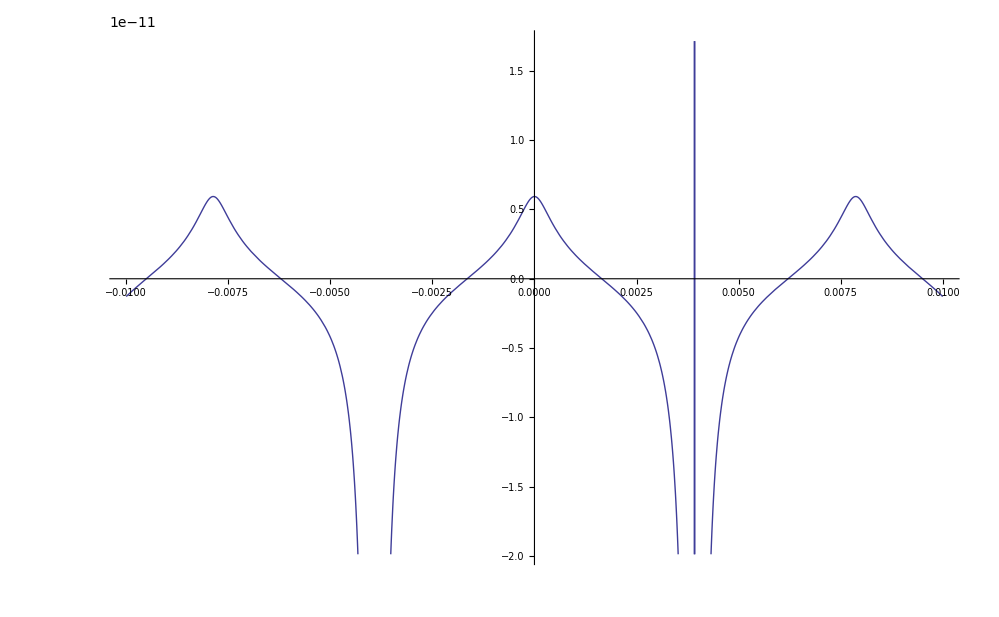

```mathematica
Plot[{(t2[L]-(Conjugate[t2[L]]) )/(2 ⅈ), },{L,-0.01,0.01}]
```

```mathematica
t3[L_,x_]:=(8 ⅇ^(-2 ⅈ x 0.5*(1+L)))/(ⅇ^(-2 ⅈ x L) x^2*A*A (2-ⅈ x*A p1) p2 p3+ⅇ^(2 ⅈ x 0.5*(1-L)) x^2*A*A p1 (2+ⅈ x*A p2) p3+x^2*A*A p1 p2 (2-ⅈ x*A p3)+ⅈ ⅇ^(-2 ⅈ x 0.5*(1+L)) (2 ⅈ+x*A p1) (2 ⅈ+x*A p2) (2 ⅈ+x*A p3)) /.JurassicPark
```

```mathematica
Plot3D[(t3[L,x]*(Conjugate[t3[L,x]]) ), {L,-0.01,0.01},{x,795,805}]
```

-Graphics3D-

```mathematica
t4[L_,x_]:=-(ⅇ^(-2 ⅈ x 0.5*(1+L)) x*A (ⅇ^(-2 ⅈ x L) x^2*A*A p1 p2 p3-ⅇ^(2 ⅈ x 0.5*(1-L)) (-2 ⅈ+x*A p1) (-2 ⅈ+x*A p2) p3+(-2 ⅈ+x*A p1) p2 (2 ⅈ+x*A p3)-ⅇ^(-2 ⅈ x 0.5*(1+L)) p1 (2 ⅈ+x*A p2) (2 ⅈ+x*A p3)))/(ⅇ^(-2 ⅈ x L) x^2*A*A (2 ⅈ+x*A p1) p2 p3-ⅇ^(2 ⅈ x 0.5*(1-L)) x^2*A*A p1 (-2 ⅈ+x*A p2) p3+x^2*A*A p1 p2 (2 ⅈ+x*A p3)-ⅇ^(-2 ⅈ x 0.5*(1+L)) (2 ⅈ+x*A p1) (2 ⅈ+x*A p2) (2 ⅈ+x*A p3)) /. JurassicPark
```

```mathematica
Plot[x/. f[L],{L,-0.01,0.01}]
```

```mathematica
central
```

```mathematica
M1[L_]:=x/.Last[FindMaximum[{(t3[L,x]*(Conjugate[t3[L,x]]) ),797<x<802},x]]
```

```mathematica
M1[0.1]
```

797.5